```mathematica
Get["C:\\Users\\tinmi\\OneDrive\\Namizje\\dn2_nror\\datoteka1.m"];
```

```mathematica
MC[n_]:=Module[{podatki},podatki=Table[datoteka1[i],{i,1,n}];
ListLinePlot[podatki,AxesLabel->{"Število poskusov","Približna vrednost π"},PlotLabel->"Izračun π",PlotRange->{3,4}]]
```

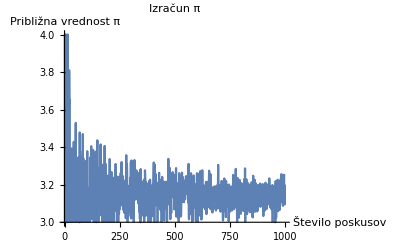

```mathematica
MC[1000]
```